```mathematica
(* Error arising from discretisting at the i^th time point, an integral of the product of terms before (i-1)/n*)
```

```mathematica
f1[n_,k_,a_,g_]:=(1 - Exp[(-2 n)/(k-1)a (g-x)])PDF[NormalDistribution[0,√((k-1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],x - g]
```

Closed form expression for survival probability of BM under a linear boundary

```mathematica
survivalprob[a_,b_,T_]:=CDF[NormalDistribution[],b √T + a/(√T)] - ⅇ^(- a b)CDF[NormalDistribution[],b √T -a/(√T)]
```

Survival probability bound in KB (2005)

```mathematica
survivalprobbound[a_,b_,T_]:=a(√(2/(π T))+2Abs[b])
```

Survival probability bound in KB (2005) is uniformly good.

```mathematica
Manipulate[Plot[{survivalprob[a,b,T],a(√(2/(π T))+2Abs[b])},{T,0,1}],{a,0,1},{b,-1,1}]
```

```mathematica
(* Error arising from discretisting at the i^th time point, an integral of the product of terms after (i+1)/n*)
```

```mathematica
f2[n_,k_,a_,g_]:= survivalprob[g-x, 1, 1 - (k+1)/n](g-x)PDF[NormalDistribution[0,1/(√n)],x-g]
```

```mathematica
f2alt[n_,k_,a_,g_]:= survivalprobbound[g-x, 1, 1 - (k+1)/n](g-x)PDF[NormalDistribution[0,1/(√n)],x-g]
```

```mathematica
nlisti[n_] := 
Table[
NIntegrate[f1[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]
```

```mathematica
nlistialt[n_] := 
Table[
NIntegrate[f1[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2alt[n,k,1,1],{x,-∞,1}],{k,2,n-2}]
```

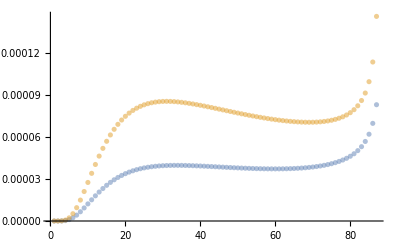

```mathematica
ListPlot[{nlisti[90],nlistialt[90]},PlotStyle->{Opacity[0.5],Opacity[0.5]}]
```

```mathematica
(* Table of errors from k = 1 to n*)
```

```mathematica
nlist[N1_,N2_,δ_] := Table[
NIntegrate[f1[n,n,1,1],{x,-∞,1}]+
NIntegrate[f2[n,1,1,1],{x,-∞,1}]+
Total[
Table[
NIntegrate[f1[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
nlist[10,20,1]
```

{0.0971403,0.0892806,0.0826047,0.0768657,0.0718806,0.0675107,0.0636491,0.0602122,0.0571335,0.0543598,0.0518478}

```mathematica
nlistv2[N1_,N2_,δ_] := Table[
NIntegrate[f1[n,n,1,1],{x,-∞,1}]+
NIntegrate[f2alt[n,1,1,1],{x,-∞,1}]+
Total[
Table[
NIntegrate[f1[n,k,1,1],{x,-∞,1}]*
NIntegrate[f2alt[n,k,1,1],{x,-∞,1}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
(* Convergence plot of ∑_(k=1)^n Subscript[Error, k]. It looks like 1/n, which is what we need. *)
```

```mathematica
nl1 = nlist[3,200,15]
```

{0.255338,0.0571335,0.0325276,0.0228479,0.0176451,0.0143884,0.0121549,0.0105264,0.00928565,0.00830851,0.00751878,0.0068671,0.00632008,0.00585431}

```mathematica
nl2 = nlistv2[3,200,15]
```

{0.64432,0.120413,0.0659439,0.0454215,0.0346468,0.0280065,0.0235034,0.0202485,0.017786,0.0158578,0.0143069,0.0130325,0.0119667,0.0110622}

```mathematica
nl1
```

{0.255338,0.0571335,0.0325276,0.0228479,0.0176451,0.0143884,0.0121549,0.0105264,0.00928565,0.00830851,0.00751878,0.0068671,0.00632008,0.00585431}

```mathematica
Table[n,{n,3,200,15}]
```

{3,18,33,48,63,78,93,108,123,138,153,168,183,198}

```mathematica
nl1/Table[1/n,{n,3,200,15}]
```

{0.766014,1.0284,1.07341,1.0967,1.11164,1.1223,1.1304,1.13685,1.14213,1.14657,1.15037,1.15367,1.15658,1.15915}

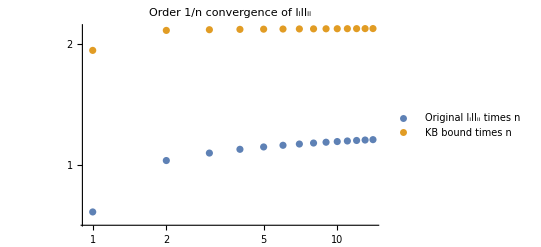

```mathematica
ListLogLogPlot[{nl1/Table[1/n,{n,3,200,15}],nl2/Table[1/n,{n,3,200,15}]},PlotLegends->{"Original I_iII_ii times n","KB bound times n"}, PlotLabel->"Order 1/n convergence of I_iII_ii"]
```

## Bounding the integrals

```mathematica
f1c[n_,k_,a_,g_]:=(2 n)/(k-1)a (g-x)^2 PDF[NormalDistribution[0,√((k-1)/n)],x]PDF[NormalDistribution[0,1/(√n)],x - g]
```

```mathematica
NIntegrate[f1c[3,2,1,1],{x,-∞,1}]
```

0.566604

```mathematica
nlistc[N1_,N2_,δ_] := Table[
Total[
Table[
NIntegrate[f1c[n,k,1,1],{x,-∞,∞}]*
NIntegrate[f2[n,k,1,1],{x,-∞,∞}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

The usual bound 1-e^-x≤ x is sufficient to retain the convergence rate. Extending the integration region for both integrals to the entire real line is also sufficient.

```mathematica
nlc = nlistc[3,200,20]
```

{0,0.0696199,0.0322201,0.0210865,0.0157108,0.0125347,0.0104342,0.0089407,0.00782363,0.00695624}

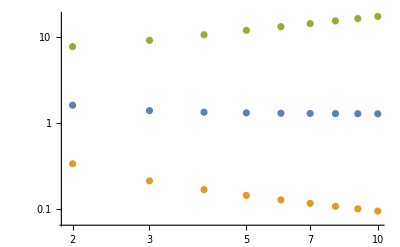

```mathematica
ListLogLogPlot[{nlc/Table[1/n,{n,3,200,20}],nlc/Table[1/(√n),{n,3,200,20}],nlc/Table[1/n^(3/2),{n,3,200,20}]}]
```

```mathematica
nlistd[N1_,N2_,δ_] := Table[
Total[
Table[
NIntegrate[f1c[n,k,1,1],{x,-∞,∞}]*
NIntegrate[f2alt[n,k,1,1],{x,-∞,∞}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
nld = nlistd[3,200,20]
```

{0,0.131955,0.0598607,0.0387475,0.0286651,0.0227545,0.0188688,0.0161189,0.01407,0.0124841}

The bounds: 
- 1-e^-x≤ x  ;
- Extending the integration region for both integrals to the entire real line ;
- P(sup_(0≤ t ≤ T) (W_t-bt) < a) ≤ a(√(2/(π T))+2|b| )

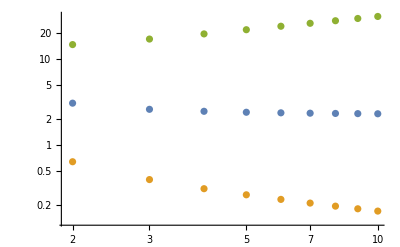

```mathematica
ListLogLogPlot[{nld/Table[1/n,{n,3,200,20}],nld/Table[1/(√n),{n,3,200,20}],nld/Table[1/n^(3/2),{n,3,200,20}]}]
```

```mathematica
(* We see that the integral is bounded uniformly above*)
```

```mathematica
Manipulate[Plot[{1/(4 k^3 √((-1+k)/n) n^(3/2) π)ⅇ^-n ((-1+k) (2 ⅇ^(((-3+2 k) n)/(2 (-1+k))) k n+ⅇ^(((-1+2 k) n)/(2 k)) √((k n)/(-1+k)) ((-1+k) k+n) √(2 π))+ⅇ^(((-1+2 k) n)/(2 k)) √(-1+k) √k √n ((-1+k) k+n) √(2 π) Erf[(√n)/(√2 √(-1+k) √k)]),
√(n/(2π k))(1/k^2+1/n)ⅇ^(-n/(2k))},{k,1,n}, PlotRange->Full],{n,3,10,1}]
```

```mathematica
n √n∫_2^(n-1) 1/(n(k-1)k^(2 +1/2))ⅇ^(-n/(2 k))ⅆk
```

n^(3/2) ∫_2^(-1+n) ⅇ^(-n/(2 k))/((-1+k) k^(5/2) n)ⅆk

```mathematica
n √n∫_1^(n-1) 1/(n k^(3/2))ⅇ^(-n/(2 k))ⅆk
```

ConditionalExpression[√(2 π) (-Erf[1/(√(2-2/n))]+Erf[(√n)/(√2)]),Re[n]>1||n∉Reals]

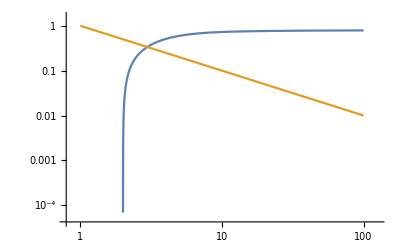

```mathematica
LogLogPlot[{√(2 π) (-Erf[1/(√(2-2/n))]+Erf[(√n)/(√2)]),1/n},{n,1,100}]
```

```mathematica
Series[x^2 ⅇ^(-1/x),{x,1,2}]
```

1/ⅇ+(3 (x-1))/ⅇ+(5 (x-1)^2)/(2 ⅇ)+O[x-1]^3

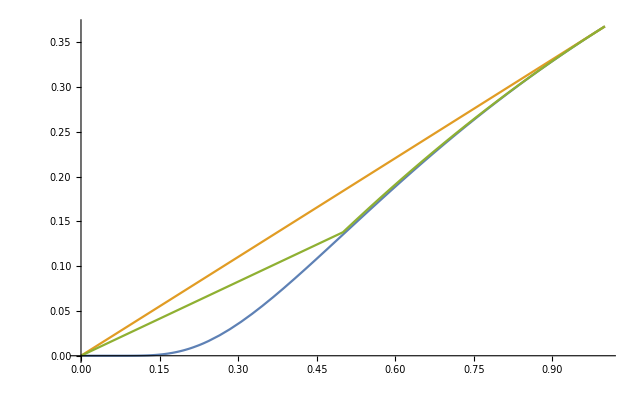

```mathematica
Plot[{ ⅇ^(-1/x),ⅇ^-1 x,1/ⅇ(x-(x-1)^2/2)If[x >1/2,1,0]+3/(4 ⅇ)x If[x <1/2,1,0] },{x,0,1}]
```

```mathematica
1/ⅇ(x-(x-1)^2/2) /. x-> 1/2
```

3/(8 ⅇ)

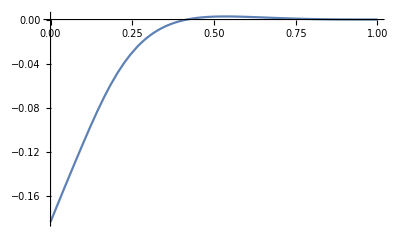

```mathematica
Plot[{1/ⅇ(x -(x-1)^2/2)-ⅇ^(-1/x)},{x,0,1}]
```

```mathematica
D[ⅇ^(-1/x),{x}]
```

ⅇ^(-1/x)/x^2

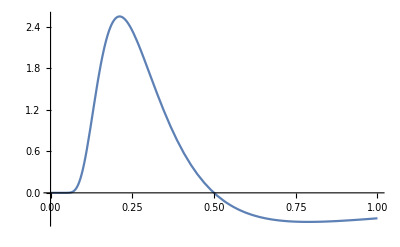

```mathematica
Plot[Evaluate[D[ⅇ^(-1/x),{x,2}]],{x,0,1}]
```

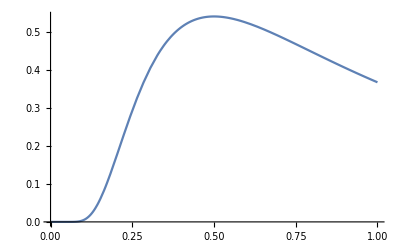

```mathematica
Plot[ⅇ^(-1/x)/x^2,{x,0,1}]
```

```mathematica
Manipulate[Plot[{ⅇ^(-n/k),(ⅇ^-1 k)/n,1/ⅇ(k/n -(k/n-1)^2/2)},{k,1,n}],{n,3,1000}]
```

```mathematica
Series[ⅇ^(-1/x),{x,1/2,2}]
```

1/ⅇ^2+(4 (x-Rational[1,2]))/ⅇ^2+O[x-Rational[1,2]]^3

```mathematica
∫_1^n ⅇ^(-n/k)ⅆk
```

ConditionalExpression[-Cosh[n]+n (1/ⅇ+ExpIntegralEi[-1])+n Gamma[0,n]+Sinh[n],(Im[n]≠0&&Re[n]≥0)||Re[n]>0]

```mathematica
∫_1^n k/n ⅆk
```

-1/(2 n)+n/2

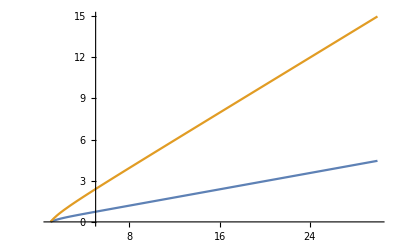

```mathematica
Plot[{-Cosh[n]+n (1/ⅇ+ExpIntegralEi[-1])+n Gamma[0,n]+Sinh[n],-1/(2 n)+n/2},{n,1,30}]
```

```mathematica
nliste[N1_,N2_,δ_] := Table[
Total[
Table[
(n/(k-1))√(n/k)*(1/k^2+1/n)ⅇ^(-n/k)
NIntegrate[f2alt[n,k,1,1],{x,-∞,∞}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

```mathematica
nle = nliste[3,200,20]
```

{0,0.591127,0.387407,0.300888,0.251572,0.219142,0.195924,0.178336,0.164464,0.153189}

```mathematica
nle = nliste[3,200,20]
```

{0,0.0514181,0.0258373,0.0173025,0.0130206,0.0104435,0.00872094,0.00748782,0.00656121,0.00583932}

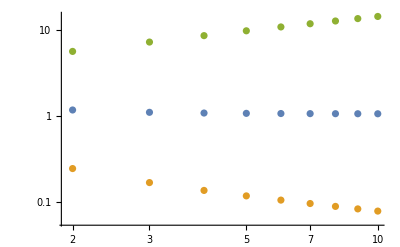

```mathematica
ListLogLogPlot[{nle/Table[1/n,{n,3,200,20}],nle/Table[1/(√n),{n,3,200,20}],nle/Table[1/n^(3/2),{n,3,200,20}]}]
```

```mathematica
nliste[N1_,N2_,δ_] := Table[
Total[
Table[
1/(k-1)√(n k)*(1/k^2+1/n)*
NIntegrate[f2alt[n,k,1,1],{x,-∞,∞}],{k,2,n-2}]],
{n,N1,N2,δ}]
```

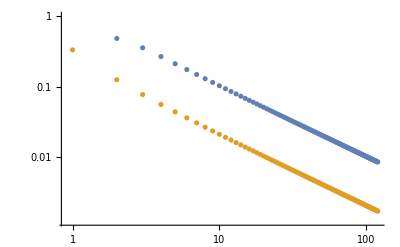

```mathematica
ListLogLogPlot[{Table[Sum[(n^(3/2)/k^(5/2))ⅇ^(-n/(2k))(√(n/(n - k -1))+1)1/n,{k,2,n-2}],{n,3,600,5}],
Table[1/n,{n,3,600,5}]}]
```

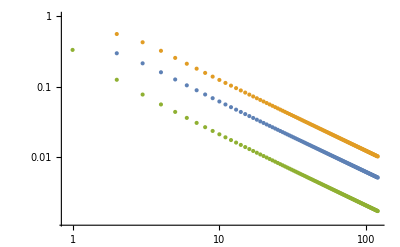

```mathematica
ListLogLogPlot[{Table[Sum[(n^(3/2)/k^(5/2))ⅇ^(-n/(2k))(√(n/(n - k -1)))1/n,{k,2,n-2}],{n,3,600,5}],
Table[Sum[(n^(3/2)/k^(5/2))ⅇ^(-n/(2k))(3)1/n,{k,2,n-2}],{n,3,600,5}],
Table[1/n,{n,3,600,5}]}]
```

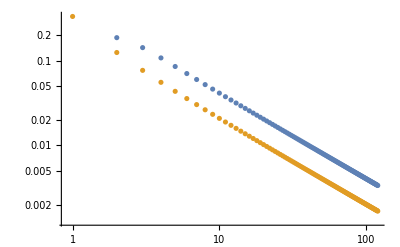

```mathematica
ListLogLogPlot[{Table[Sum[(n^(3/2)/k^(5/2))ⅇ^(-n/(2k))(1)1/n,{k,2,n-2}],{n,3,600,5}],
Table[1/n,{n,3,600,5}]}]
```

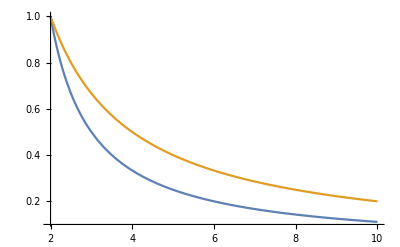

```mathematica
Plot[{1/(x-1),2/x},{x,2,10}]
```

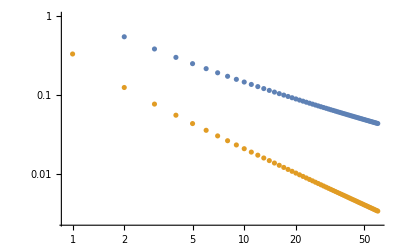

```mathematica
ListLogLogPlot[{Table[∑_(k=2)^(n-2) (√((n k)/(k-1)^2)*(1/k^2+1/n)1/n(√(n/(n-k-1)))),{n,3,300,5}],
Table[1/n,{n,3,300,5}]}]
```

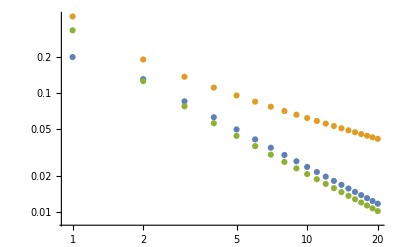

```mathematica
ListLogLogPlot[{Table[NIntegrate[1/(√(k(n-k)))(1/k^2+1/n)(2k ⅇ^-1)/n,{k,1,n-1}],{n,3,100,5}],
Table[(ⅇ^(-n/(-1+n)) (1/(-1+n)^2+1/n) (1+√n))/(√((-1+n) n))n,{n,3,100,5}],
Table[1/n,{n,3,100,5}]}]
```

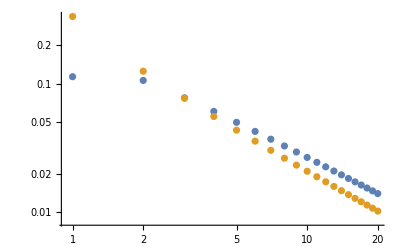

```mathematica
ListLogLogPlot[{Table[NIntegrate[1/(√(k(n-k)))(1/n)k/n,{k,1,n-1}],{n,3,100,5}],
Table[1/n,{n,3,100,5}]}]
```

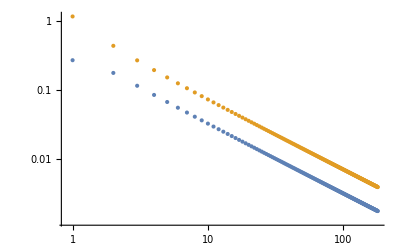

```mathematica
ListLogLogPlot[{Table[NIntegrate[1/(√(k(n-k)))(1/k^2+1/n)k/n,{k,1,n-1}],{n,3,900,5}],
Table[3.5/n,{n,3,900,5}]}]
```

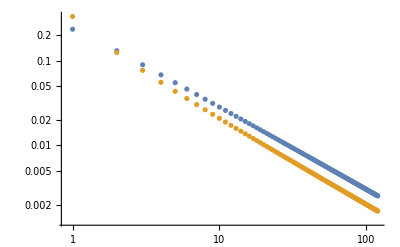

```mathematica
ListLogLogPlot[{Table[∑_(k=1)^(n-1) 1/(√(k(n-k)))(1/n)k/n,{n,3,600,5}],
Table[1/n,{n,3,600,5}]}]
```

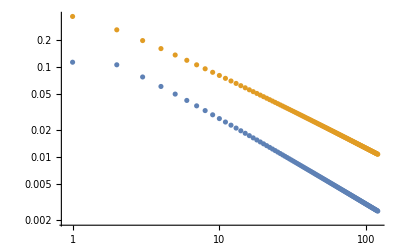

```mathematica
ListLogLogPlot[{Table[NIntegrate[1/(√(k(n-k)))(1/n)k/n,{k,1,n-1}],{n,3,600,5}],
Table[Log[n]/n,{n,3,600,5}]}]
```

```mathematica
ListLogLogPlot[{Table[NIntegrate[1/(√(k(n-k)))(1/n)k/n,{k,1,n-1}],{n,3,300,5}],
Table[1/n,{n,3,300,5}]}]
```

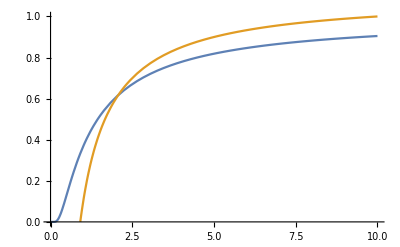

```mathematica
Plot[{ⅇ^(-1/x),1.1-1/x},{x,0,10},PlotRange->{{0,10},{0,1}}]
```

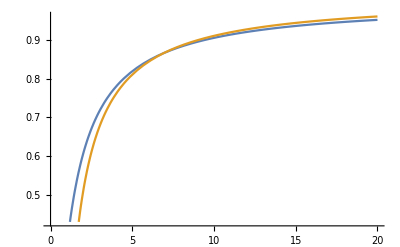

```mathematica
Plot[{ⅇ^(-1/x),1.01-1/x},{x,0,20}]
```

## EMSF implies exponentially quick convergence for linear boundaries

```mathematica
(* f[y] is the integrand where we want to take partial derivatives for the EMSF*)
```

```mathematica
f[y_]:=(1 - Exp[-2 n(Subscript[g, i+1]-Subscript[x, i+1])(Subscript[g, i]-y)])PDF[NormalDistribution[0,1/(√n)],Subscript[x, i+1]-y]*(1 - Exp[-2 n(Subscript[g, i]-y)(Subscript[g, i-1]-Subscript[x, i-1])])PDF[NormalDistribution[0,1/(√n)],Subscript[x, i-1]-y]
```

```mathematica
(* First Partial derivative is 0 *)
```

```mathematica
Evaluate[D[f[y],{y,1}]]/. y-> Subscript[g, i]
```

0

```mathematica
(* Second partial derivative is skipped in the EMSF, because it is multiplied by the Bernoulli number Subscript[B, 3] = 0. Since the Bernoulli numbers Subscript[B, n] are 0 for all odd n, we skip all the even order partial derivatives. *)
```

```mathematica
Evaluate[D[f[y],{y,2}]]/. y-> Subscript[g, i]//FullSimplify
```

(4 ⅇ^(-1/2 n ((g_i-x_(-1+i))^2+(g_i-x_(1+i))^2)) n^3 (-g_(-1+i)+x_(-1+i)) (-g_(1+i)+x_(1+i)))/π

```mathematica
(* Third partial derivatives depends on the second derivative through the (Subscript[g, -1+i]-2 Subscript[g, i]+Subscript[g, 1+i]) term*)
```

```mathematica
Evaluate[D[f[y],{y,3}]]/. y-> Subscript[g, i] //FullSimplify
```

(12 ⅇ^(-1/2 n ((g_i-x_(-1+i))^2+(g_i-x_(1+i))^2)) n^4 (g_(-1+i)-2 g_i+g_(1+i)) (-g_(-1+i)+x_(-1+i)) (-g_(1+i)+x_(1+i)))/π

```mathematica
(* Third partial derivative is zero for linear boundaries, because the (Subscript[g, -1+i]-2 Subscript[g, i]+Subscript[g, 1+i]) term is a finite difference approximation of the second derivative. *)
```

```mathematica
Evaluate[D[f[y],{y,3}]]/. y-> Subscript[g, i] /. Subscript[g, i+1]-> Subscript[g, i] + K/n /. Subscript[g, i-1]-> Subscript[g, i] - K/n //FullSimplify
```

0

```mathematica
(* In fact it appears that the odd derivatives zero whenever the boundaries a linear. This implies that the residual error must be Exponential *)
```

```mathematica
Table[Evaluate[D[f[y],{y,M}]]/. y-> Subscript[g, i] /. Subscript[g, i+1]-> Subscript[g, i] + K/n /. Subscript[g, i-1]-> Subscript[g, i] - K/n //FullSimplify ,{M,1,15,2}]
```

{0,0,0,0,0,0,0,0}